```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

```mathematica
NotebookDirectory[]
```

/Users/Fridtjof.Brauns/KITP/GBE/Experiment Data/Data Tomer/eLife Code/Snail/

#### Mesh export/import setup

```mathematica
exportTimeseriesHDF5[file_,data_]:=With[{numDigits=Ceiling[Log10[Length[data]]]},
Export[file,Table["TP"<>IntegerString[t,10,numDigits]->data[[t]],{t,Length[data]}],"Datasets"]
];
```

```mathematica
padRaggedArray[array_,pad_:0]:=With[{maxLength=Max[Length/@array]},PadRight[#,maxLength,pad]&/@array]
```

```mathematica
flattenAssociation[assoc_]:=Flatten/@List@@@Normal[assoc]
```

```mathematica
ClearAll[removePadding];
removePadding[list:{_Integer..},pad_:0]:=With[{
pos=FirstPosition[Reverse[list],Except[pad],1,Heads->False]
},
If[pos==={},(* everything is padding *)
{},
list[[1;;-First[pos]]]
]
];
removePadding[array_,pad_:0]/;Depth[array]>=3:=removePadding[#,pad]&/@array;
```

```mathematica
toAssoc[data:{{__}..}]:=Association[First[#]->Rest[#]&/@data];
```

```mathematica
importHDF5Timeseries[file_]:=With[{data=Import[file,"Data"]},
Values[KeySort[data]]
]
```

#### Load mesh data from h5 files

```mathematica
baseDir=NotebookDirectory[]<>"../../Data/Snail/Tracked Meshes/";
```

Check that the files are there

```mathematica
FileNames[baseDir<>"*.h5"]//Length
```

8

```mathematica
cellVerticesTS=EchoTiming[toAssoc/@removePadding[importHDF5Timeseries[baseDir<>"cellVertices.h5"]]];
cellNeighborsTS=EchoTiming[toAssoc/@removePadding[importHDF5Timeseries[baseDir<>"cellNeighbors.h5"]]];
cellCentroidsTS=EchoTiming[toAssoc/@importHDF5Timeseries[baseDir<>"cellCentroids.h5"]];
vertexCoordsTS=EchoTiming[importHDF5Timeseries[baseDir<>"vertexCoords.h5"]];
vertex2DCoordsTS=EchoTiming[importHDF5Timeseries[baseDir<>"vertexCoords2D.h5"]];
vertexCellsTS=EchoTiming[removePadding[importHDF5Timeseries[baseDir<>"vertexCells.h5"]]];
vertexCellsTS=EchoTiming[removePadding[importHDF5Timeseries[baseDir<>"vertexNeighbors.h5"]]];
edgeVerticesTS=EchoTiming[removePadding[importHDF5Timeseries[baseDir<>"edgeVertices.h5"]]];
```

1.5455

1.48524

0.2774

0.080354

0.082692

3.92735

4.04006

5.83669

#### Generate cell pair contact timetraces

For each pair of cells that are ever neighbors, generate a time trace indicating whether they are neighbors (0 - no, 1 - yes) and whether both cells exists (-1 if not).

In these timetraces, we can then look for events. 

We can then spatially and temporally correlate these events to identify proper neighbor exchanges.

```mathematica
allNeighborAssoc=Union[Flatten[#]]&/@Association[Last@Reap[
KeyValueMap[Sow[#2,#1];&,#]&/@cellNeighborsTS,
_,Rule
]];//AbsoluteTiming
```

{0.292485,Null}

```mathematica
Take[allNeighborAssoc,4]
```

<|1→{2,5},2→{1,3,5,13,17},3→{2,13,17,32},4→{8,21,38,44,52}|>

```mathematica
contactPairs=Union[Sort/@Catenate[KeyValueMap[Thread[{#1,#2}]&,allNeighborAssoc]]];
```

```mathematica
Length@contactPairs
```

9159

```mathematica
pairContactTS=Association[Thread[contactPairs->Transpose@Map[Function[{neighborAssoc},
Map[Function[{pair},
If[
KeyExistsQ[neighborAssoc,pair[[1]]]&&
KeyExistsQ[neighborAssoc,pair[[2]]],
If[MemberQ[neighborAssoc[pair[[1]]],pair[[2]]],1,0],
-1
]
],
contactPairs
]
],
cellNeighborsTS
]]];//AbsoluteTiming
```

{2.66852,Null}

#### Permanent pairs

```mathematica
permanentPairs=Keys[Select[pairContactTS,Union[#]=={1}&]];
```

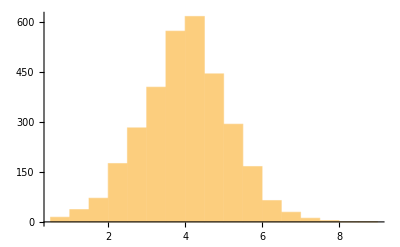

```mathematica
Histogram[sharedEdgeLength[#,1]&/@permanentPairs]
```

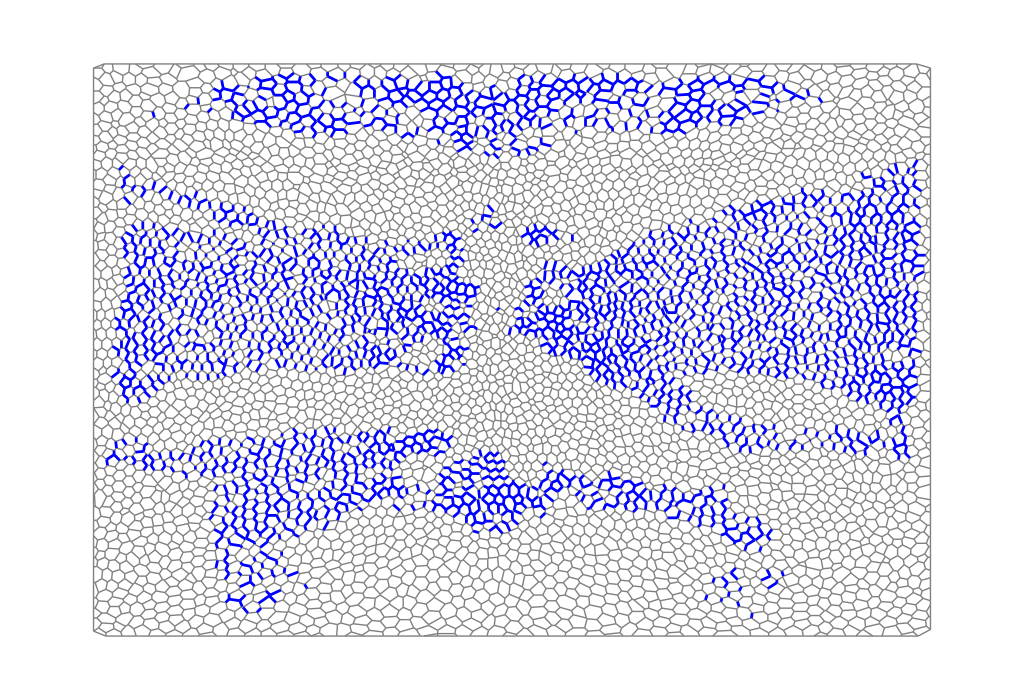

```mathematica
Graphics[
GraphicsComplex[vertex2DCoordsTS[[1]],{
Gray,Line[edgeVerticesTS[[1]]],
AbsoluteThickness[2],Blue,
Line[sharedVertices[#,1]]&/@permanentPairs
}
]
]
```

#### Collapses

```mathematica
allFirstCollapses=Select[
If[#[[1]]==1,First@FirstPosition[#,0,{-1}],-1]&/@pairContactTS,
Positive
];
```

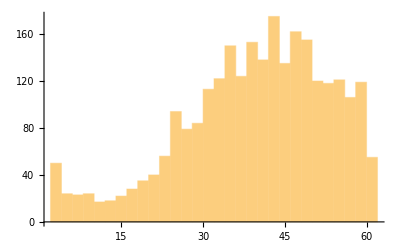

```mathematica
Histogram[allFirstCollapses,{2}]
```

#### Permanent collapses

```mathematica
persistentCollapses=Select[
If[#[[1]]==1&&#[[-1]]==0,First@FirstPosition[#,0,{-1}],-1]&/@pairContactTS,
Positive
];
```

```mathematica
persistentCollapses//Length
```

2262

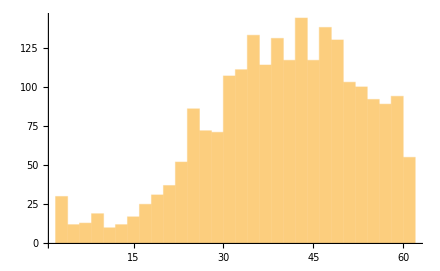

```mathematica
Histogram[persistentCollapses,{2}]
```

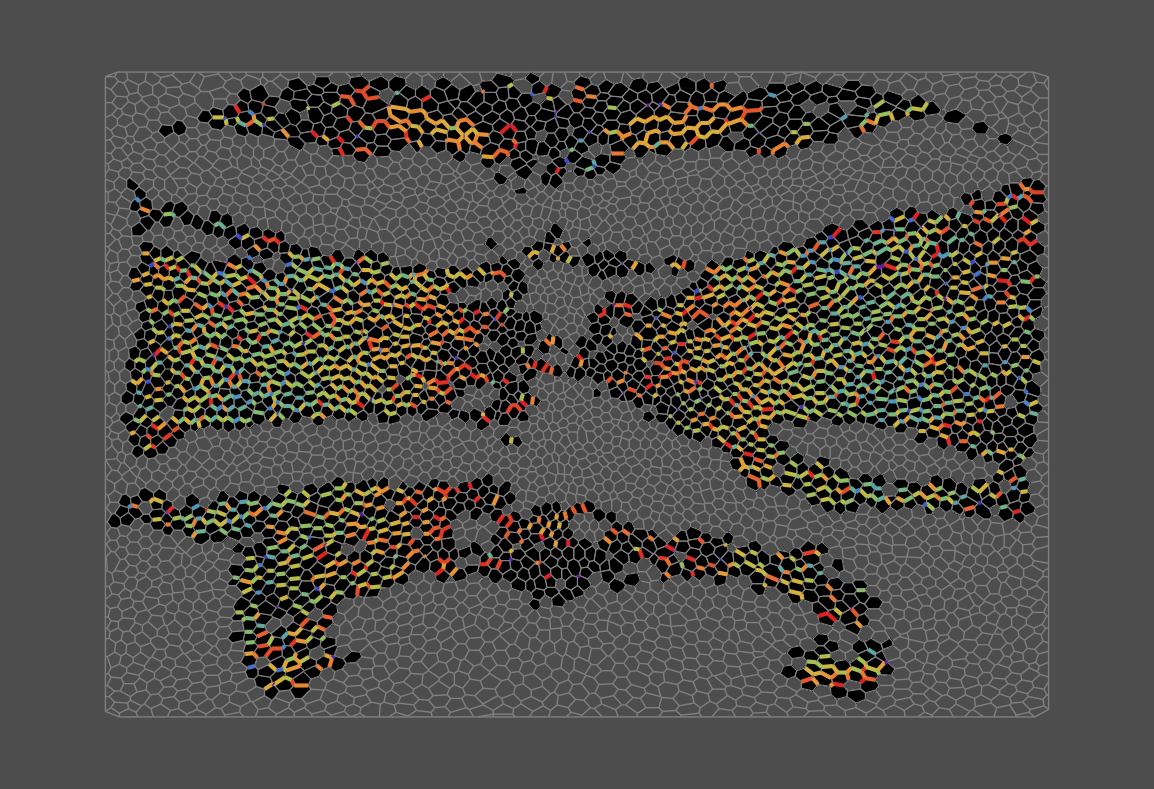

```mathematica
Graphics[{
GraphicsComplex[vertex2DCoordsTS[[1]],{
Gray,Line[edgeVerticesTS[[1]]],
EdgeForm[Gray],FaceForm[Black],
Polygon[cellVerticesTS[[1]][#]]&/@Range[Length[cellNeighborsTS[[1]]]],
AbsoluteThickness[3],
Map[
Function[event,{ColorData["Rainbow"][(event[[2]])/60],Line[sharedVertices[event[[1]],1]]}],
Reverse@SortBy[Normal[persistentCollapses],Last]
]
}]},
Background->GrayLevel[0.3]
]
```

```mathematica
collapseCounts=With[{cells=Flatten[Keys[persistentCollapses]]},{#,Count[cells,#]}&/@Union[cells]];
```

```mathematica
Max[collapseCounts[[All,2]]]
```

6

```mathematica
collapseCounts[[4]]
```

{11,1}

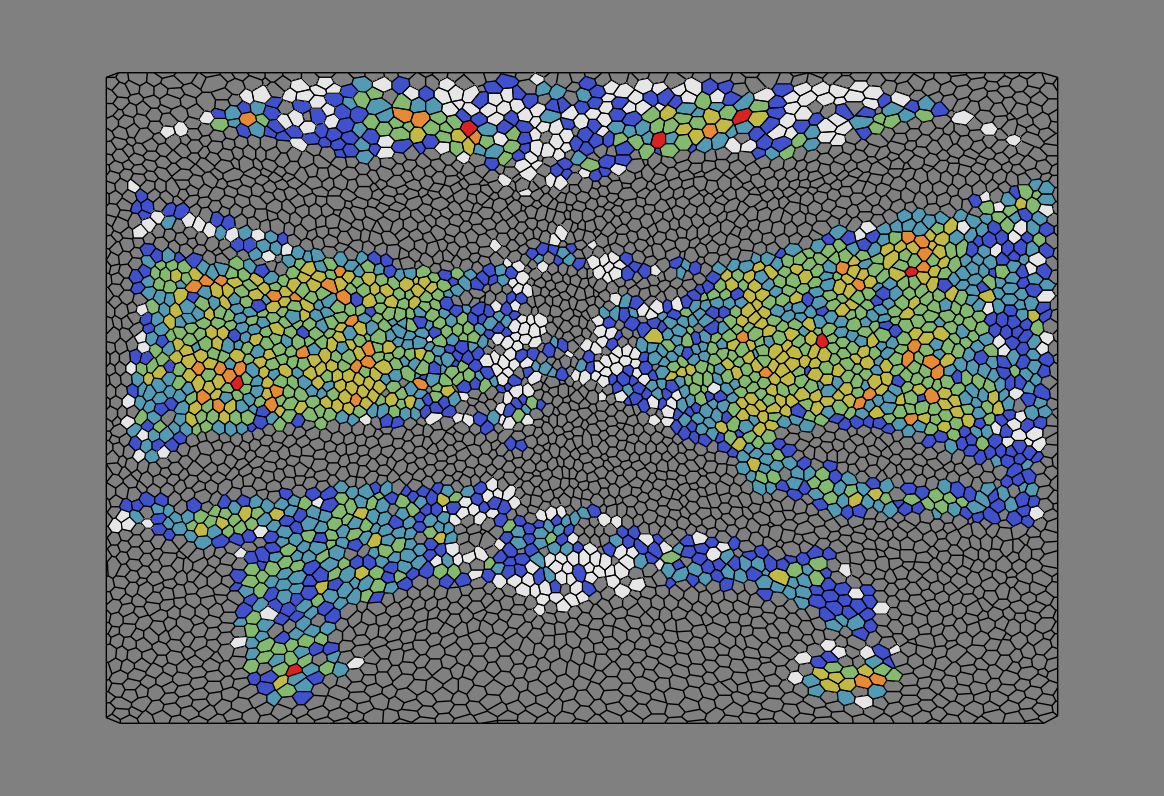

```mathematica
Graphics[{
GraphicsComplex[vertex2DCoordsTS[[1]],{
Black,Line[edgeVerticesTS[[1]]],
EdgeForm[Black],
Map[
{ColorData["Rainbow"][(#[[2]])/6],Polygon[cellVerticesTS[[1]][#[[1]]]]}&,
collapseCounts
],
GrayLevel[0.9],
Polygon[cellVerticesTS[[1]][#]]&/@Complement[Range[Length[cellNeighborsTS[[1]]]],collapseCounts[[All,1]]]
}]},
Background->GrayLevel[0.5]
]
```

#### Collapsing edge length

```mathematica
edgeLengthData=KeyValueMap[
Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2-1}]&,
persistentCollapses
];//AbsoluteTiming
```

{1.16459,Null}

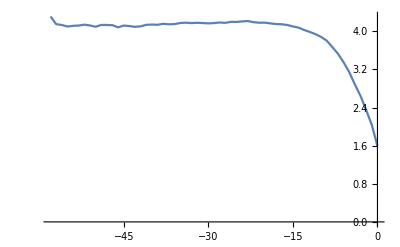

```mathematica
ListLinePlot[averageTimeseries[edgeLengthData],PlotRange->All]
```

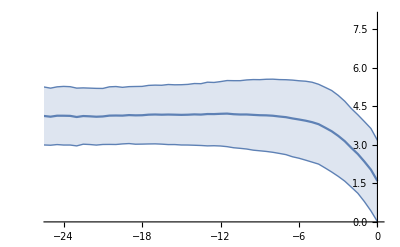

```mathematica
collapseLengthPlot=ListLinePlot[{
{#[[1]]/2,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@binByFirst[Catenate[edgeLengthData]]
},
IntervalMarkers->"Bands",
PlotRange->{{-25,0},{0,8}}
]
```

No transient extension. Confirms that extension in WT is driven by VF invagination.

#### Relative tension

```mathematica
edgeTensionData=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,1,#2-1}]&,
persistentCollapses
]];//AbsoluteTiming
```

{16.1281,Null}

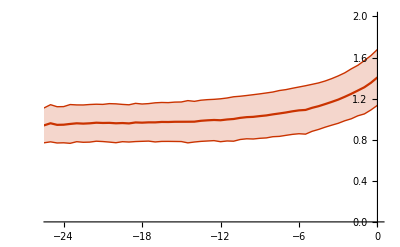

```mathematica
collapseTensionPlot=With[{
tensionData=binByFirst[Catenate[DeleteCases[
(* filter out missing data due to degenerate vertices and very short edges (< 0.75µm) *)
({#[[1]],#[[2,2]]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[edgeTensionData],
{}
]]]},
ListLinePlot[
{#[[1]]/2,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[tensionData,#[[1]]>=-100&&Length[#[[2]]]>10&],
IntervalMarkers->"Bands",
PlotRange->{{-25,0},{0,2}},
PlotStyle->ColorData[112,1]
]
]
```

#### Edge creation

```mathematica
edgeCreationEventsRaw=Select[
If[#[[1]]==0&&#[[-1]]==1,First@FirstPosition[#,1,{-1}],-1]&/@pairContactTS,
Positive
];
```

Exclude events where no common neighbor existed in the two timestep before the contact. These events are typically due to invaginations

```mathematica
excludeEvents=keyValueSelect[
edgeCreationEvents,
Intersection@@(cellNeighborsTS[[#2-2]]/@#1)==={}||Intersection@@(cellNeighborsTS[[#2-1]]/@#1)==={}&
];
```

```mathematica
edgeCreationEvents=KeyDrop[edgeCreationEventsRaw,Keys[excludeEvents]];
```

```mathematica
Length[edgeCreationEvents]
```

2001

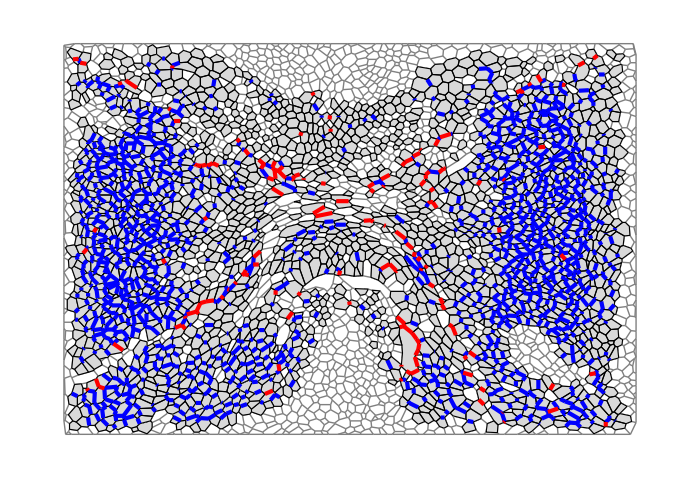

```mathematica
Graphics[{
GraphicsComplex[vertex2DCoordsTS[[-1]],{
Gray,Line[edgeVerticesTS[[-1]]],
EdgeForm[Black],FaceForm[LightGray],
Polygon[cellVerticesTS[[-1]][#]]&/@Range[Length[cellNeighborsTS[[-1]]]],
AbsoluteThickness[3],Blue,
Line[sharedVertices[#,-1]]&/@Keys[edgeCreationEvents],
Red,
Line[sharedVertices[#,-1]]&/@Keys[excludeEvents]
}
]
},
ImageSize->700
]
```

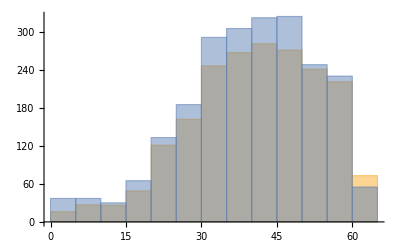

```mathematica
Histogram[{
edgeCreationEvents,
persistentCollapses
},{5},PerformanceGoal->"Speed"]
```

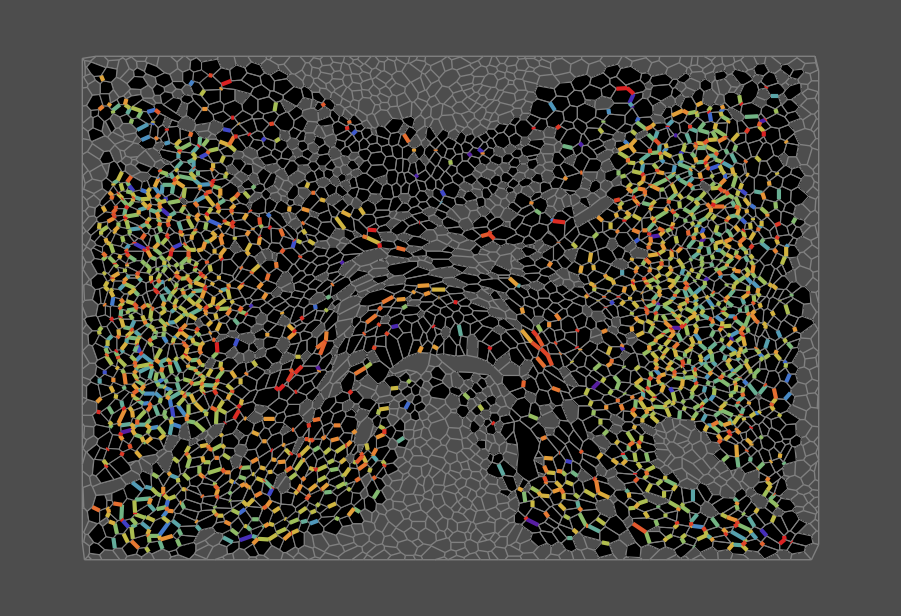

```mathematica
Graphics[{
GraphicsComplex[vertex2DCoordsTS[[-1]],{
Gray,Line[edgeVerticesTS[[-1]]],
EdgeForm[Gray],FaceForm[Black],
Polygon[cellVerticesTS[[-1]][#]]&/@Range[Length[cellNeighborsTS[[-1]]]],
AbsoluteThickness[3],
Map[
Function[event,{ColorData["Rainbow"][event[[2]]/60],Line[sharedVertices[event[[1]],-1]]}],
SortBy[Normal[edgeCreationEvents],Last]
]
}]},
Background->GrayLevel[0.3]
]
```

#### Length

```mathematica
edgeLengthData=KeyValueMap[
DeleteCases[Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2,60}],{_,0}]&,
edgeCreationEvents
];//AbsoluteTiming
```

{0.573647,Null}

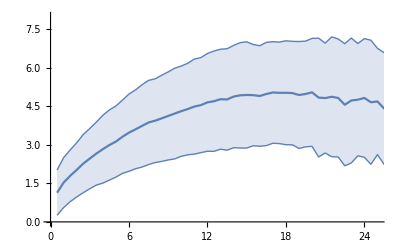

```mathematica
newEdgeLengthPlot=ListLinePlot[{
{#[[1]]/2,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@binByFirst[Catenate[edgeLengthData]]
},
IntervalMarkers->"Bands",
PlotRange->{{0,25},{0,8}}
]
```

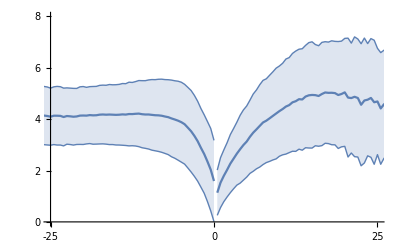

```mathematica
Show[collapseLengthPlot,newEdgeLengthPlot,PlotRange->{{-25,25},{0,8}},AxesOrigin->{-25,0},Ticks->{{-25,0,25},Range[0,8,2]}]
```

#### Tension

```mathematica
newEdgeTensionData=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,#2,60}]&,
KeyDrop[edgeCreationEvents,{{1485,1554},{1717,1779},{1752,1810}}]
]];//AbsoluteTiming
```

{7.76315,Null}

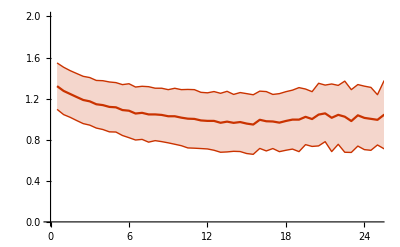

```mathematica
newEdgeTensionPlot=With[{
tensionData=binByFirst@Catenate[
({#[[1]],Clip[#[[2,2]],{0,2}]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[newEdgeTensionData]]},
ListLinePlot[{#[[1]]/2,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[tensionData,#[[1]]<=100&&Length[#[[2]]]>10&],
IntervalMarkers->"Bands",
PlotStyle->ColorData[112,1],
PlotRange->{{0,25},{0,2}}
]
]
```

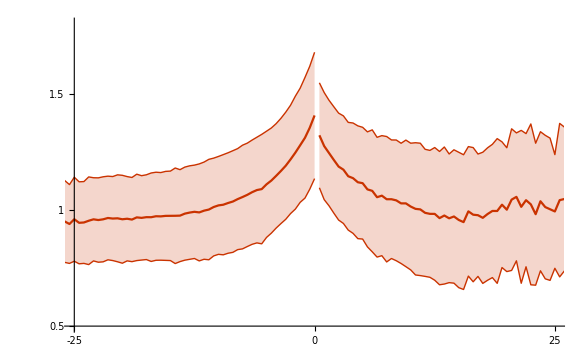

```mathematica
Show[collapseTensionPlot,newEdgeTensionPlot,PlotRange->{{-25,25},{0.5,1.8}},AxesOrigin->{-25,0.5},Ticks->{{-25,0,25},{0.5,1,1.5}}]
```